# Lab 1 Math 151 Calculus

## Markiyan Varhola, Section 02

## Problems

The first four problems below are fairly routine, but they all contain ideas about limits that you need to know for our course.

1.	The function f(x)=(sin(x))/x is called the “sinc” function. 
	a)	Create a table of values to find lim_(x→ 0) (sin(x))/x	
	b)	Plot f(x) on the interval [-6,6]
	c)	Is f(x) as defined a continuous function? What is f(0)?
	d) 	Compute  lim_(x→ 0) (sin(x))/x using Mathematica
	e)	How would you define f(0) in order to remove the discontinuity?
	f)	Are there any algebraic calculations you can do to find lim_(x→ 0) (sin(x))/x that don’t already involve further ideas from 	calculus?  If yes, do them using Mathematica!
	
	
A)

```mathematica
Table[Sin[1/n]/(1/n),{n,1,20}]//N
```

{0.841471,0.958851,0.981584,0.989616,0.993347,0.995377,0.996602,0.997398,0.997944,0.998334,0.998623,0.998843,0.999014,0.99915,0.999259,0.999349,0.999423,0.999486,0.999538,0.999583}

B)

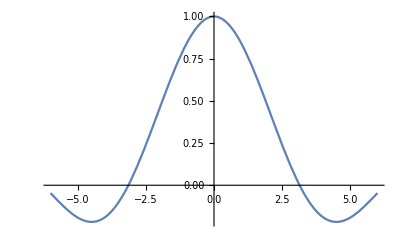

```mathematica
Plot[Sin[x]/x,{x,-6,6}]
```

C) No, it is not continuous, as f(0) is undefined

D)

```mathematica
Limit[Sin[x]/x,x->0]
```

E) f(0)=1
F) No, unless you know the squeeze theorem.

2.	Consider the function f(x)=(1-cos(x))/x  
	a)	Create a table of values to find lim_(x→ 0) (1-cos(x))/x
	b)	Plot f(x) on the interval [-6,6]
	c)	Is f(x) as defined a continuous function? What is f(0)?
	d) 	Compute  lim_(x→ 0) (1-cos(x))/x using Mathematica
	e)	How would you define f(0) in order to remove the discontinuity?
	f)	Are there any algebraic calculations you can do to find lim_(x→ 0) (1-cos(x))/x that don’t already involve further ideas from calculus?  If yes, do them using Mathematica!

A)

```mathematica
Table[(1-Cos[1/n])/(1/n),{n,1,20}]//N
```

{0.459698,0.244835,0.165129,0.12435,0.0996671,0.0831406,0.0713072,0.0624187,0.0554984,0.0499583,0.0454232,0.0416426,0.0384426,0.0356991,0.033321,0.0312398,0.0294033,0.0277706,0.0263097,0.0249948}

B)

```mathematica
Plot[(1-Cos[x])/x,{x,-6,6}]
```

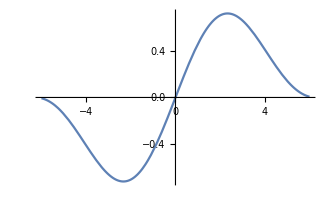

C) No, it is not continuous, as f(0) is undefined

D)

```mathematica
Limit[(1-Cos[x])/x,x->0]
```

0

E) f(0) = 0
F) No.

3.	Consider the function f(x)=(1+x)^(1/x)  
	a)	Create a table of values to find lim_(x→ 0) (1+x)^(1/x)
	b)	Plot f(x) on the interval [0,6]
	c)	Is f(x) as defined a continuous function? What is f(0)?
	d) 	Compute  lim_(x→ 0) (1+x)^(1/x) using Mathematica
	e)	How would you define f(0) in order to remove the discontinuity?
	f)	Are there any algebraic calculations you can do to find lim_(x→ 0) (1+x)^(1/x) that don’t already involve further ideas 	from calculus?  If yes, do them using Mathematica!
	
A)

```mathematica
Table[(1+1/x)^(1/(1/n)),{n,1,20}]//N
```

{1.+1/x,(1.+1/x)^2,(1.+1/x)^3,(1.+1/x)^4,(1.+1/x)^5,(1.+1/x)^6,(1.+1/x)^7,(1.+1/x)^8,(1.+1/x)^9,(1.+1/x)^10,(1.+1/x)^11,(1.+1/x)^12,(1.+1/x)^13,(1.+1/x)^14,(1.+1/x)^15,(1.+1/x)^16,(1.+1/x)^17,(1.+1/x)^18,(1.+1/x)^19,(1.+1/x)^20}

B)

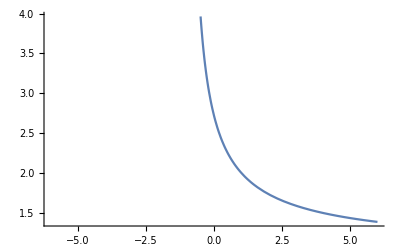

```mathematica
Plot[(1+x)^(1/x),{x,-6,6}]
```

C) The function is not continuous, f(0) is undefined

```mathematica
f[x_]:=(1+x)^(1/x)
```

```mathematica
f[0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1^ComplexInfinity encountered.

```mathematica
Indeterminate
```

D) f(0) = e
F) No.

4.	Consider the function f(x)=((2+x)^3-8)/x  
	a)	Create a table of values to find lim_(x→ 0) ((2+x)^3-8)/x
	b)	Plot f(x) on the interval [0,6]
	
	c)	Is f(x) as defined a continuous function? What is f(0)?
	d) 	Compute  lim_(x→ 0) ((2+x)^3-8)/x using Mathematica
	e)	How would you define f(0) in order to remove the discontinuity?
	f)	Are there any algebraic calculations you can do to find lim_(x→ 0) ((2+x)^3-8)/x that don’t already involve further ideas from calculus? If yes, do them using Mathematica!

A).

```mathematica
Table[((2+1/n)^3-8)/(1/n),{n,1,20}]
```

{19,61/4,127/9,217/16,331/25,469/36,631/49,817/64,1027/81,1261/100,1519/121,1801/144,2107/169,2437/196,2791/225,3169/256,3571/289,3997/324,4447/361,4921/400}

B).

Plot[((2+n)^3-8)/n,{n,0,6}]

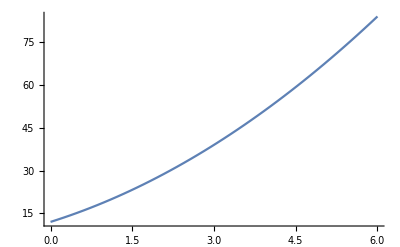

C). No,

```mathematica
((2+0)^3-8)/0
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

```mathematica
Indeterminate
```

D).

```mathematica
Limit[((2+n)^3-8)/n,x->0]
```

12+6 n+n^2

E) f(0)=12

```mathematica
((2+0.00000001)^3-8)/0.00000001
```

12.

F).

```mathematica
Simplify[((2+n)^3-8)/n]
```

12+6 n+n^2

```mathematica
Limit[12+6 n+n^2,n->0]
```

12

5.	Verify that the the slope of the tangent line to the function f(x)=-x^3 + x^2+ 12x- 3 from the Manipulate above at x=0, is the same as what you would get if you used the D 	operator. Now do the same for x=1, 2, and 3.

```mathematica
D[-x^3 + x^2+ 12x- 3,x]
```

12+2 x-3 x^2

```mathematica
(12+2 x-3 x^2)/.x->0
```

12

```mathematica
(12+2 x-3 x^2)/.x->1
```

11

```mathematica
(12+2 x-3 x^2)/.x->2
```

4

```mathematica
(12+2 x-3 x^2)/.x->3
```

-9

6.	Use the Manipulate above to try and estimate where the slope of the tangent line is equal to zero, then figure out where 	this happens using the commands built into 	Mathematica and compare your estimate to the value you found. We will be spending a great deal of time doing this sort of calculation. You will need to use the N 		function to get some decimals at some point.

```mathematica
D[-x^3 + x^2+ 12x- 3,x]
```

12+2 x-3 x^2

```mathematica
x/.Solve[12+2x-3 x^2==0,x]
```

{1/3 (1-√37),1/3 (1+√37)}

```mathematica
Solve[12+2 x-3 x^2==0,x]
```

{{x→1/3 (1-√37)},{x→1/3 (1+√37)}}

```mathematica
N[{{x->1/3 (1-√37)},{x->1/3 (1+√37)}}]
```

{{x→-1.69425},{x→2.36092}}